```mathematica
(*ClearAll["Global`*"]*)
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/cop.txt";
data = Import[path, "Data"];
```

```mathematica
lsquared=50*50;
iterationsReported = 500;
Manipulate[
ListPlot[
Select[Take[data,{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported-1,1}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[data,{1,lsquared}].

Part::partd: Part specification data⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of {1,lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Take::normal: Nonatomic expression expected at position 1 in Take[data,{1,lsquared}].

Part::partd: Part specification data⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of {1,lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

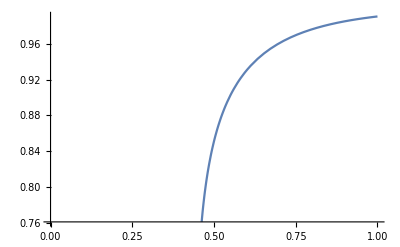

{0.0743315,0.925668,0.851337}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{beta→-0.441379},{beta→0.441379}}

```mathematica
m[beta_] := (1-Csch[2*beta*1]^2)^(1/8);
Plot[m[beta],{beta,0,1}]
{(1-m[0.5])/2,(1+m[0.5])/2,m[0.5]}
Solve[(1-Csch[2*beta*1]^2)^(1/8)==0.5,beta]
```